Variables Initiation

```mathematica
s1=0.01;
s2=0.19;
s3=0.07666666718652951;
a3=0.14666666562694088;
s4=0.0720000006565245;
a4=0.1119999990152132;
Msat=1.36 10^6; 
μ0=4π 10^-7;
cr1r2 = (8 Msat^2 π r^3 r^3 μ0)/9;
Clear[a,s,r,r1,r2,r3,r4,a,b,c,d,k,v];
kineticEnergy[r_,n_]:={

crr = (8 Msat^2 π r^3 r^3 μ0*10^6)/9; (* cr1r2 is a constant includes all the terms except the distance between the spheres*)
Msat=1.36 10^6; 
μ0=4π 10^-7;

{ke,b1,c1}=With[{z=NMaximize[{crr(1/(2*10r)^3)+crr(1/(2*10r)^3-1/(a+10r)^3)*(n-1)-crr *(1/(2*10r+s)^3*n),s≥0,a≥ s,10(4n+2)r+n*s+(n-1)a== 10},{s,a},Method->"SimulatedAnnealing"]},Extract[z,Position[z,_?NumericQ]]];

ke/10^3


};
```

```mathematica
6*1.430807501968882+1.4151549881867076
```

10.

n = 1 Optimum Value Calculation

```mathematica
Clear[r,a,s]
NMaximize[{cr1r2(1/(2r)^3)+cr1r2(1/(2r)^3-1/(a+r)^3)*0-cr1r2 *(1/(2r+s)^3*1),s≥0,a≥0,10/6≥ r>0,6r+s==10},{r,s,a},Method->"SimulatedAnnealing"]
```

{1.6646×10^6,{r→1.43081,s→1.41515,a→0.909427}}

n = 1 Plot

NMaximize::bcons: The following constraints are not valid: {60 m+s==10,a≥s,s≥0}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

Set::shape: Lists {ke,b1,c1} and {0.,8.11325×10^8,3,-6.4906×10^12,6,20,-3,0,60,10} are not the same shape.

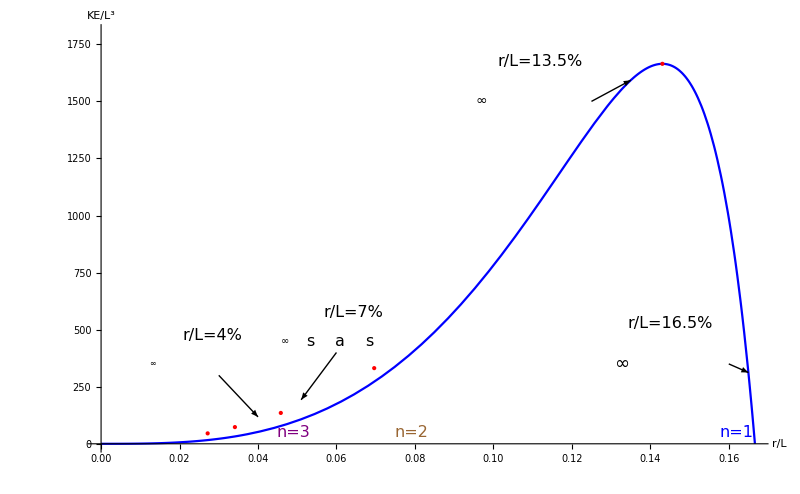

```mathematica
n1=Plot[kineticEnergy[m,1],{m,0.00001,1/6},AxesLabel->{"r/L","KE/L^3"},PlotStyle->Blue,PlotRange->{{0,1800}},LabelStyle->{FontSize->18,Bold,Black},AxesStyle->Thick,ImageSize->800,Epilog->{Red,PointSize[Large],Point[{{0.1430807501968882,1.6645954663256719*^3},{0.06961977577658549,331.46589342817},{0.04581323180896628,135.20530680423474},{0.034113436101682143,73.15117149758207},{0.02716726455741465,45.628249293290035}}],Arrowheads[Medium],Black,Arrow[{{0.16,350},{0.165,312.214624394686}}],Arrow[{{0.125,1500},{0.135,1592.5060580958936}}],Black,Arrow[{{0.06,400},{0.051,192.87333677637537}}],Black,Arrow[{{0.03,+300},{0.040,117.9228685250036}}],Text[Style["r/L=16.5%",Black,16,Italic],{0.14495000000000002,350+175}],Text[Style["r/L=13.5%",Black,16,Italic],{0.112,1500+175}],Text[Style["r/L=7%",Black,16,Italic],{0.064225,400+175}],Text[Style["r/L=4%",Black,16,Italic],{0.0285,300+175}],
Text[Style["s",Black,16,Italic],{0.05+(0.03*0.07*2+s3*0.03)/2,450}],Text[Style["a",Black,16,Italic],{0.05+(0.03*0.07*2+s3*0.03)+(0.03*0.07*2+a3*0.03)/2,450}],Text[Style["s",Black,16,Italic],{0.05+(0.03*0.07*2+s3*0.03)+(0.03*0.07*2+a3*0.03)+(0.03*0.07*2+s3*0.03)/2,450}],
Text[Style["n=1",Blue,16,Italic],{0.162,+50}],Text[Style["n=2",Brown,16,Italic],{0.079,+50}],Text[Style["n=3",Purple,16,Italic],{0.049,+50}](*,Text[Style["n=4",Pink,16,Italic],{0.049,+50}]*),
Text[Style["∞",Black,18,Italic],{00.14-1.5*0.165*0.03,350}],Text[Style["∞",Black,14,Italic],{(00.103-3*0.03*0.135+00.103)/2,1500}],
Text[Style["∞",Black,10,Italic],{(00.05-3*0.03*0.07+00.05)/2,450}],Text[Style["∞",Black,8,Italic],{(0.015-3*0.03*0.04+0.015)/2,350}]}]
```

n = 2 Optimum Value Calculation

```mathematica
Clear[r,a,s]
NMaximize[{cr1r2(1/(2r)^3)+cr1r2(1/(2r)^3-1/(a+r)^3)*1-cr1r2 *(1/(2r+s)^3*2),s≥0,a≥ 0,10/10≥ r>0,10r+2s+a==10},{r,s,a},Method->"SimulatedAnnealing"]
```

{331466.,{r→0.696198,s→0.780608,a→1.47681}}

n = 2 Plot

NMaximize::bcons: The following constraints are not valid: {a+100 m+2 s==10,a≥s,s≥0}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

Set::shape: Lists {ke,b1,c1} and {8.11325×10^8,3,6.4906×10^12,6,1/8000,-3,-1,10,-3,-1.29812×10^13,6,20,-3,0,100,2,10} are not the same shape.

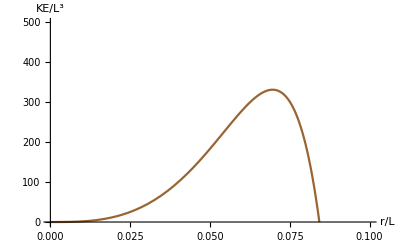

```mathematica
n2=Plot[kineticEnergy[m,2],{m,0.00001,0.1},AxesLabel->{"r/L","KE/L^3"},PlotStyle->Brown,PlotRange->{{0,500}}]
```

n = 3 Optimum Value Calculation

```mathematica
NMaximize[{cr1r2(1/(2r)^3)+cr1r2(1/(2r)^3-1/(a+r)^3)*2-cr1r2 *(1/(2r+s)^3*3),s≥0,a≥ s,10/12≥ r>0,14r+3s+2a==10},{r,s,a},Method->"SimulatedAnnealing"]
```

{135666.,{r→0.458132,s→0.533977,a→0.992109}}

n = 3 Plot

NMaximize::bcons: The following constraints are not valid: {2 a+140 m+3 s==10,a≥s,s≥0}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

Set::shape: Lists {ke,b1,c1} and {8.11325×10^8,3,1.29812×10^13,6,1/8000,-3,-1,10,-3,-1.94718×10^13,6,20,-3,0,2,140,3,10} are not the same shape.

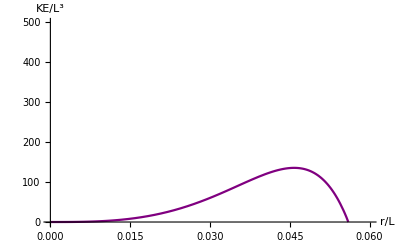

```mathematica
n3=Plot[kineticEnergy[m,3],{m,0.00001,0.06},AxesLabel->{"r/L","KE/L^3"},PlotStyle->Purple,PlotRange->{{0,500}}]
```

n = 4 Optimum Value Calculation

```mathematica
NMaximize[{cr1r2(1/(2r)^3)+cr1r2(1/(2r)^3-1/(a+r)^3)*3-cr1r2 *(1/(2r+s)^3*4),s≥0,a≥ s,10/18≥ r>0,18r+4s+3a==10},{r,s,a},Method->"SimulatedAnnealing"]
```

{73151.2,{r→0.341134,s→0.405168,a→0.746303}}

n = 4 Plot

NMaximize::bcons: The following constraints are not valid: {3 a+180 m+4 s==10,a≥s,s≥0}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

Set::shape: Lists {ke,b1,c1} and {8.11325×10^8,3,1.94718×10^13,6,1/8000,-3,-1,10,-3,-2.59624×10^13,6,20,-3,0,3,180,4,10} are not the same shape.

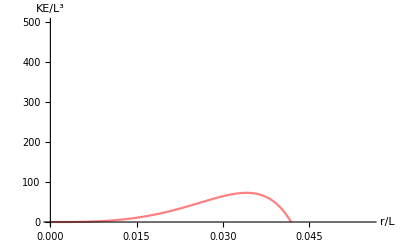

```mathematica
n4=Plot[kineticEnergy[m,4],{m,0.00001,1/18},AxesLabel->{"r/L","KE/L^3"},PlotStyle->Pink,PlotRange->{{0,500}}]
```

n = 5 Optimum Value Calculation

```mathematica
NMaximize[{cr1r2(1/(2r)^3)+cr1r2(1/(2r)^3-1/(a+r)^3)*4-cr1r2 *(1/(2r+s)^3*5),s≥0,a≥ s,10/22≥ r>0,22r+5s+4a==10},{r,s,a},Method->"SimulatedAnnealing"]
```

{45628.2,{r→0.271673,s→0.326279,a→0.597952}}

n = 5 Plot

NMaximize::bcons: The following constraints are not valid: {4 a+220 m+5 s==10,a≥s,s≥0}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

Set::shape: Lists {ke,b1,c1} and {8.11325×10^8,3,2.59624×10^13,6,1/8000,-3,-1,10,-3,-3.2453×10^13,6,20,-3,0,4,220,5,10} are not the same shape.

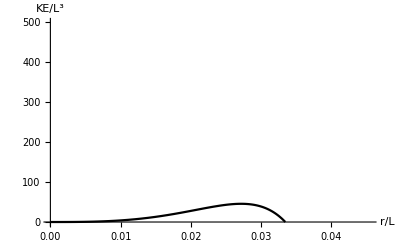

```mathematica
n5=Plot[kineticEnergy[m,5],{m,0.00001,1/22},AxesLabel->{"r/L","KE/L^3"},PlotStyle->Black,PlotRange->{{0,500}}]
```

n = 6 Optimum Value Calculation

```mathematica
NMaximize[{cr1r2(1/(2r)^3)+cr1r2(1/(2r)^3-1/(a+r)^3)*5-cr1r2 *(1/(2r+s)^3*6),s≥0,a≥ s,10/26≥ r>0,26r+6s+5a==10},{r,s,a},Method->"SimulatedAnnealing"]
```

{31143.5,{r→0.225691,s→0.273054,a→0.498744}}

n = 6 Plot

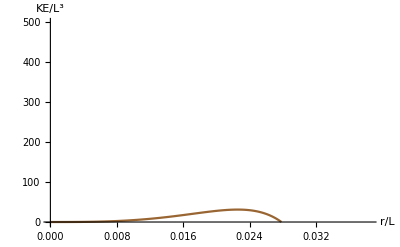

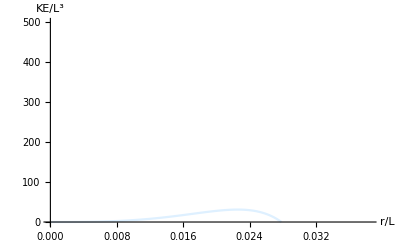

```mathematica
n6=Plot[kineticEnergy[m,6],{m,0.00001,1/26},AxesLabel->{"r/L","KE/L^3"},PlotStyle->LightBlue,PlotRange->{{0,500}}]
```

n = 7 Optimum Value Calculation

```mathematica
NMaximize[{cr1r2(1/(2r)^3)+cr1r2(1/(2r)^3-1/(a+r)^3)*6-cr1r2 *(1/(2r+s)^3*7),s≥0,a≥ s,10/30≥ r>0,30r+7s+6a==10},{r,s,a},Method->"SimulatedAnnealing"]
```

{22598.9,{r→0.193011,s→0.234738,a→0.427749}}

n = 7 Plot

NMaximize::bcons: The following constraints are not valid: {6 a+300 m+7 s==10,a≥s,s≥0}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

Set::shape: Lists {ke,b1,c1} and {8.11325×10^8,3,3.89436×10^13,6,1/8000,-3,-1,10,-3,-4.54342×10^13,6,20,-3,0,6,300,7,10} are not the same shape.

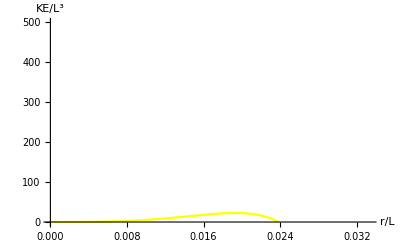

```mathematica
n7=Plot[kineticEnergy[m,7],{m,0.00001,1/30},AxesLabel->{"r/L","KE/L^3"},PlotStyle->Yellow,PlotRange->{{0,500}}]
```

n = 8 Optimum Value Calculation

```mathematica
NMaximize[{cr1r2(1/(2r)^3)+cr1r2(1/(2r)^3-1/(a+r)^3)*7-cr1r2 *(1/(2r+s)^3*8),s≥0,a≥ s,10/34≥ r>0,34r+8s+7a==10},{r,s,a},Method->"SimulatedAnnealing"]
```

{17141.4,{r→0.168594,s→0.205842,a→0.374436}}

n = 8 Plot

NMaximize::bcons: The following constraints are not valid: {7 a+340 m+8 s==10,a≥s,s≥0}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

Set::shape: Lists {ke,b1,c1} and {8.11325×10^8,3,4.54342×10^13,6,1/8000,-3,-1,10,-3,-5.19248×10^13,6,20,-3,0,7,340,8,10} are not the same shape.

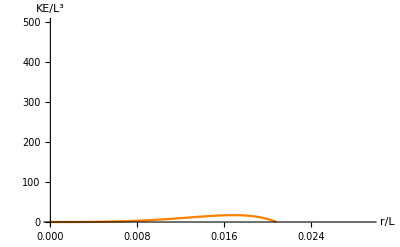

```mathematica
n8=Plot[kineticEnergy[m,8],{m,0.00001,1/34},AxesLabel->{"r/L","KE/L^3"},PlotStyle->Orange,PlotRange->{{0,500}}]
```

n = 9 Optimum Value Calculation

```mathematica
NMaximize[{cr1r2(1/(2r)^3)+cr1r2(1/(2r)^3-1/(a+r)^3)*8-cr1r2 *(1/(2r+s)^3*9),s≥0,a≥ s,10/38≥ r>0,38r+9s+8a==10},{r,s,a},Method->"SimulatedAnnealing"]
```

{13445.5,{r→0.149659,s→0.183275,a→0.332934}}

n = 9 Plot

NMaximize::bcons: The following constraints are not valid: {8 a+380 m+9 s==10,a≥s,s≥0}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

Set::shape: Lists {ke,b1,c1} and {8.11325×10^8,3,5.19248×10^13,6,1/8000,-3,-1,10,-3,-5.84154×10^13,6,20,-3,0,8,380,9,10} are not the same shape.

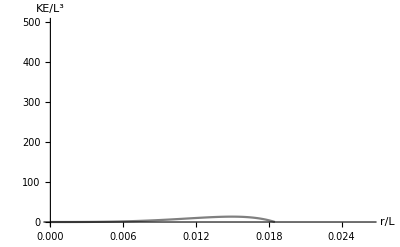

```mathematica
n9=Plot[kineticEnergy[m,9],{m,0.00001,1/38},AxesLabel->{"r/L","KE/L^3"},PlotStyle->Gray,PlotRange->{{0,500}}]
```

n = 10 Optimum Value Calculation

```mathematica
NMaximize[{cr1r2(1/(2r)^3)+cr1r2(1/(2r)^3-1/(a+r)^3)*9-cr1r2 *(1/(2r+s)^3*10),s≥0,a≥ s,10/42≥ r>0,42r+10s+9a==10},{r,s,a},Method->"SimulatedAnnealing"]
```

{10827.5,{r→0.134546,s→0.165165,a→0.299711}}

n = 10 Plot

NMaximize::bcons: The following constraints are not valid: {9 a+420 m+10 s==10,a≥s,s≥0}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

Set::shape: Lists {ke,b1,c1} and {8.11325×10^8,3,5.84154×10^13,6,1/8000,-3,-1,10,-3,-6.4906×10^13,6,20,-3,0,9,420,10,10} are not the same shape.

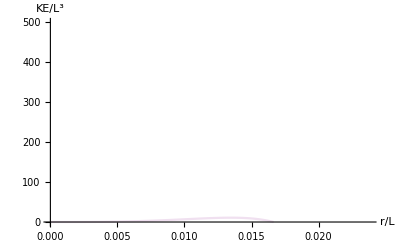

```mathematica
n10=Plot[kineticEnergy[m,10],{m,0.00001,1/42},AxesLabel->{"r/L","KE/L^3"},PlotStyle->LightPurple,PlotRange->{{0,500}}]
```

Random

```mathematica
NMaximize[{cr1r2(1/(2r)^3-1/(a+r)^3)*5-cr1r2 *(1/(2r+s)^3*5),s≥0,a≥ s,10/22≥ r>0,22r+5s+4a==10},{r,s,a},Method->"SimulatedAnnealing"]
```

{42158.1,{r→0.264872,s→0.324152,a→0.638013}}

```mathematica
{a,{b,c}}=NMinimize[{x-y,-3 x^2+2 x y-y^2≥-1},{x,y}]/.sol:{__Rule}:>Values[sol]
```

{-1.,{2.7693×10^-17,1.}}

```mathematica
a
```

-1.

```mathematica
b
```

2.7693×10^-17

```mathematica
c
```

1

```mathematica
Clear[a]
```

```mathematica
{v=#,{b,c,d}=Values[#2]}&@@
NMaximize[{cr1r2(1/(2r)^3-1/(a+r)^3)-cr1r2 *(1/(2r+s)^3*2),s≥0,a≥ s,r==0.5,8r+2s+a==10},{r,s,a},Method->"SimulatedAnnealing"]
```

```mathematica
{88039.45154644968,{0.5000000000000007,1.833333344391038,2.3333333112179195}}
d
```

{88039.5,{0.5,1.83333,2.33333}}

2.33333

```mathematica
{a=#,{b,c}=Values[#2]}&@@Minimize[{x-y,-3 x^2+2 x y-y^2≥-1},{x,y}]
```

{-1,{0,1}}

```mathematica
a
```

-1

```mathematica
b
```

0

```mathematica
r1=100;r2=40;r3=70;r4=70;r=70;a=147;s=70;
```

```mathematica
a
```

a

```mathematica
a
```

```mathematica
v
```

3.31466×10^14

```mathematica
PEbefore[r_,a_,s_]:=cr1r2(1/(2r+s)^3+ 1/(2r+a)^3+ 1/(4r+a+s)^3+1/(2 r+s)^3+1/(4r+a+s)^3 +1/(6r+a+2s)^3);
PEafter[r_,a_,s_]:=cr1r2(1/(2 r)^3+1/(2r+a+s)^3 )
```

```mathematica
PEbefore[1,1,1]
```

790180. r^6

```mathematica
PEafter[1,1,1]
```

912741. r^6

```mathematica
NMinimize[{(8 Msat^2 π r^3 r^3 μ0)/9(1/(2 r)^3)-(8 Msat^2 π r^3 r^3 μ0)/9(1/(2r+s)^3+),s≥r,a≥ 0,10/8≥ r>0,8r+2s+a==10},{r,s,a},Method->"SimulatedAnnealing"]
```

{0.000179301,{r→0.000604592,s→2.30307,a→5.38902}}

```mathematica
NMaximize[{cr1r2(1/(2r)^3-1/(a+r)^3)-cr1r2 *(1/(2r+s)^3*2),s≥0,a≥ s,10/8≥ r>0,8r+2s+a==10},{r,s,a},Method->"SimulatedAnnealing"]
```

{152880.,{r→0.696243,s→1.2446,a→1.94085}}

```mathematica
kineticEnergy[0.002323]
```

{0.0203409}

```mathematica
{a1,b1,c1,d1}=With[{z=NMaximize[{cr1r2(1/(2r)^3)+cr1r2(1/(2r)^3-1/(a+r)^3)*1-cr1r2 *(1/(2r+s)^3*2),s≥0,a≥ 0,10/10≥ r>0,10r+2s+a==10},{r,s,a},Method->"SimulatedAnnealing"]},Extract[z,Position[z,_?NumericQ]]]
```

{331466.,0.696198,0.780608,1.47681}

```mathematica
a
```

-1

```mathematica
d
```

2.33333

The Plot

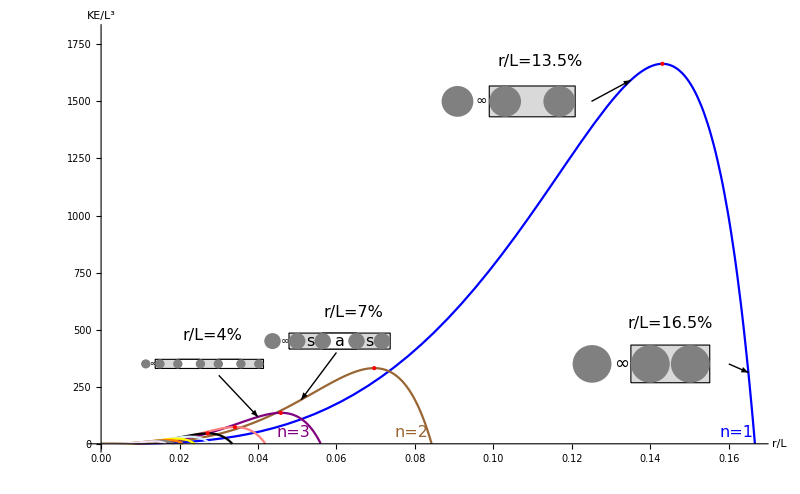

```mathematica
Cir1=Graphics[{Gray,Disk[{00.14,+350},{0.03*0.165,500*0.165}],Disk[{00.14+0.03*0.165*2+s1*0.03,+350},{0.03*0.165,500*0.165}]}];

Cir1a=Graphics[{Gray,Disk[{00.14-3*0.03*0.165,350},{0.03*0.165,500*0.165}]}];

Cir2=Graphics[{Gray,Disk[{00.103,+1500.00},{0.03*0.135,500*0.135}],Disk[{00.103+0.03*0.135*2+s2*0.03,+1500.00},{0.03*0.135,500*0.135} ]}];

Cir2a=Graphics[{Gray,Disk[{00.103-3*0.03*0.135,+1500.00},{0.03*0.135,500*0.135}]}];

Cir3 = Graphics[{Gray,Disk[{00.05,+450},{0.03*0.07,0.07*500}],Disk[{00.05+0.03*0.07*2+s3*0.03,+450},{0.03*0.07,0.07*500} ],Disk[{00.05+0.03*0.07*4+a3*0.03+s3*0.03,+450},{0.03*0.07,0.07*500}],Disk[{00.05+0.03*0.07*6+s3*0.03+a3*0.03+s3*0.03,+450},{0.03*0.07,0.07*500}]}];

Cir3a = Graphics[{Gray,Disk[{00.05-3*0.03*0.07,+450},{0.03*0.07,0.07*500}]}];

Cir4 = Graphics[{Gray,Disk[{0.015,+350},{0.03*0.04,500*0.04}],Disk[{0.015+0.03*0.04*2+s4*0.03,+350},{0.03*0.04,500*0.04} ],Disk[{0.015+0.03*0.04*4+a4*0.03+s4*0.03,+350},{0.03*0.04,500*0.04}],Disk[{0.015+0.03*0.04*6+a4*0.03+s4*0.03*2,+350},{0.03*0.04,500*0.04}],
Disk[{0.015+0.03*0.04*8+a4*0.03*2+s4*0.03*2,+350},{0.03*0.04,500*0.04}],Disk[{0.015+0.03*0.04*10+a4*0.03*2+s4*0.03*3,+350},{0.03*0.04,500*0.04}]}];

Cir4a = Graphics[{Gray,Disk[{0.015-3*0.03*0.04,+350},{0.03*0.04,500*0.04}]}];

rect1=Graphics[{FaceForm[LightGray],EdgeForm[{Thick,Black}],Rectangle[{00.14-0.03*0.165,350-500*0.165
},{00.14+0.03*0.165*3+s1*0.03,+350+500*0.165
}]}];

rect2=Graphics[{FaceForm[LightGray],EdgeForm[{Thick,Black}],Rectangle[{00.103-0.03*0.135,+1500.00-500*0.135
},{00.103+0.03*0.135*3+s2*0.03,+1500.00+500*0.135
}]}];

rect3=Graphics[{FaceForm[LightGray],EdgeForm[{Thick,Black}],Rectangle[{00.05-0.03*0.07,+450-0.07*500
},{00.05+0.03*0.07*7+(a3+s3+s3)*0.03,+450+0.07*500}]}];

rect3a=Graphics[{FaceForm[White],EdgeForm[{Thick,Black}],Rectangle[{00.05+0.03*0.07*2+s3*0.03*1,+450-0.07*500
},{00.05+0.03*0.07*4+a3*0.03+s3*0.03,+450+0.07*500}]}];

rect4=Graphics[{FaceForm[LightGray],EdgeForm[{Thick,Black}],Rectangle[{0.015-0.03*0.04,+350-500*0.04
},{0.015+0.03*0.04*11+a4*0.03*2+s4*0.03*3,+350+500*0.04}]}];

rect4a=Graphics[{FaceForm[White],EdgeForm[{Thick,Black}],Rectangle[{0.015+0.03*0.04*2+s4*0.03*1,+350-500*0.04
},{0.015+0.03*0.04*3+s4*0.03+a3*0.03,+350+500*0.04}]}];

rect4b=Graphics[{FaceForm[White],EdgeForm[{Thick,Black}],Rectangle[{0.015+0.03*0.04*6+a4*1*0.03+s4*0.03*2,+350-500*0.04
},{0.015+0.03*0.04*8+a4*1*0.03*2+s4*0.03*2,+350+500*0.04}]}];


Show[n1,n2,n3,n4,n5,n6,n7,n8,n9,n10,rect1,Cir1,rect2,Cir2,Cir2a,rect3,rect3a,Cir1a,Cir3a,Cir4a,Cir3,rect4,rect4a,rect4b,Cir4]
```

different radii for n=1

```mathematica
NMaximize[{(8 Msat^2 π r^3 r1^3 μ0)/9(1/(r+r1)^3)-(8 Msat^2 π r1^3 r2^3 μ0)/9(1/(r1+r2+s)^3),s≥0,10/6≥ r>0,10/6≥ r1>0,10/6≥ r2>0,2r+2r1+2r2+s==10},{r,r1,r2,s},Method->"SimulatedAnnealing"]
```

{3.75614×10^6,{r→1.66667,r1→1.66667,r2→0.000665587,s→3.332}}

different radii for n=2 (doesn’t work well)

```mathematica
NMaximize[{(8 Msat^2 π r^3 r1^3 μ0)/9(1/(r+r1)^3)+(8 Msat^2 π r2^3 r3^3 μ0)/9(1/(r2+r3)^3)-(8 Msat^2 π r2^3 r3^3 μ0)/9(1/(r2+r3+a)^3)-(8 Msat^2 π r1^3 r2^3 μ0)/9(1/(r1+r2+s)^3)-(8 Msat^2 π r3^3 r4^3 μ0)/9(1/(r3+r4+s)^3),s≥0,a≥s,1000/10≥ r>0,1000/10≥ r1>0,1000/10≥ r2>0,1000/10≥ r3>0,1000/10≥ r4>0,2r+2r1+2r2+2r3+2r4+2s+a==1000},{r,r1,r2,r3,r4,a,s},Method->{"SimulatedAnnealing", Tolerance->1/10000000000000000}]
```

{-7.4706×10^11,{r→99.9895,r1→100.,r2→98.2141,r3→100.,r4→100.,a→1.3523,s→1.12017}}

```mathematica
(8 Msat^2 π r^3 r1^3 μ0)/9(1/(r+r1)^3)+(8 Msat^2 π r2^3 r3^3 μ0)/9(1/(r2+r3)^3)-(8 Msat^2 π r2^3 r3^3 μ0)/9(1/(r2+r3+a)^3)-(8 Msat^2 π r1^3 r2^3 μ0)/9(1/(r1+r2+s)^3)-(8 Msat^2 π r3^3 r4^3 μ0)/9(1/(r3+r4+s)^3)
```

4.24485×10^11

different radii for n=3

```mathematica
NMaximize[{(8 Msat^2 π r^3 r1^3 μ0)/9(1/(r+r1)^3)+(8 Msat^2 π r2^3 r3^3 μ0)/9(1/(r2+r3)^3)-(8 Msat^2 π r2^3 r3^3 μ0)/9(1/(r2+r3+a)^3)-(8 Msat^2 π r1^3 r2^3 μ0)/9(1/(r1+r2+s)^3)-(8 Msat^2 π r3^3 r4^3 μ0)/9(1/(r3+r4+s)^3),s≥0,a>s,1000/10≥ r>0,1000/10≥ r1>0,1000/10≥ r2>0,1000/10≥ r3>0,1000/10≥ r4>0,2r+2r1+2r2+2r3+2r4+2s+a==1000},{r,r1,r2,r3,r4,a,s},Method->"SimulatedAnnealing"]
```

{-7.4706×10^11,{r→99.9895,r1→100.,r2→98.2141,r3→100.,r4→100.,a→1.3523,s→1.12017}}

```mathematica
(8 Msat^2 π r^3 r1^3 μ0)/9(1/(r+r1)^3)+(8 Msat^2 π r2^3 r3^3 μ0)/9(1/(r2+r3)^3)-(8 Msat^2 π r2^3 r3^3 μ0)/9(1/(r2+r3+a)^3)-(8 Msat^2 π r1^3 r2^3 μ0)/9(1/(r1+r2+s)^3)-(8 Msat^2 π r3^3 r4^3 μ0)/9(1/(r3+r4+s)^3)
```

4.24485×10^11

```mathematica
r1=100;r2=40;r3=70;r4=70;r=70;a=147;s=70;
```

```mathematica
a
```

a

```mathematica
a
```

```mathematica
v
```

3.31466×10^14

```mathematica
PEbefore[r_,a_,s_]:=cr1r2(1/(2r+s)^3+ 1/(2r+a)^3+ 1/(4r+a+s)^3+1/(2 r+s)^3+1/(4r+a+s)^3 +1/(6r+a+2s)^3);
PEafter[r_,a_,s_]:=cr1r2(1/(2 r)^3+1/(2r+a+s)^3 )
```

```mathematica
PEbefore[1,1,1]
```

790180. r^6

```mathematica
PEafter[1,1,1]
```

912741. r^6

```mathematica
NMinimize[{(8 Msat^2 π r^3 r^3 μ0)/9(1/(2 r)^3)-(8 Msat^2 π r^3 r^3 μ0)/9(1/(2r+s)^3+),s≥r,a≥ 0,10/8≥ r>0,8r+2s+a==10},{r,s,a},Method->"SimulatedAnnealing"]
```

{0.000179301,{r→0.000604592,s→2.30307,a→5.38902}}

```mathematica
NMaximize[{cr1r2(1/(2r)^3-1/(a+r)^3)-cr1r2 *(1/(2r+s)^3*2),s≥0,a≥ s,10/8≥ r>0,8r+2s+a==10},{r,s,a},Method->"SimulatedAnnealing"]
```

{152880.,{r→0.696243,s→1.2446,a→1.94085}}

```mathematica
kineticEnergy[0.002323]
```

{0.0203409}

```mathematica
{a1,b1,c1,d1}=With[{z=NMaximize[{cr1r2(1/(2r)^3)+cr1r2(1/(2r)^3-1/(a+r)^3)*1-cr1r2 *(1/(2r+s)^3*2),s≥0,a≥ 0,10/10≥ r>0,10r+2s+a==10},{r,s,a},Method->"SimulatedAnnealing"]},Extract[z,Position[z,_?NumericQ]]]
```

{331466.,0.696198,0.780608,1.47681}

```mathematica
a
```

-1

```mathematica
kineticEnergy[0.04,3]
```

```mathematica
{117.9228685250036}
b1
c1
```

{117.923}

0.72

1.12

```mathematica
{331.34334537800925}
```

```mathematica
{331.34334537800925}
b1
c1
```

{331.343}

0.766667

1.46667

```mathematica
{1592.5060580958936}
b1
```

{1592.51}

0.1

```mathematica
{312.214624394686}
```

{312.215}

0.1

```mathematica
00.14-0.03*0.165+00.14+0.03*0.165*3
```

```mathematica
0.28990000000000005/2
```

0.14495

```mathematica
b1
```

1.9

```mathematica
00.103-0.03*0.135+00.103+0.03*0.135*3
```

0.2141

```mathematica
0.21409999999999998/2
```

0.10705

```mathematica
0.015-0.03*0.04+0.015+0.03*0.04*11+a4*0.03*2+s4*0.03*3
```

```mathematica
0.05519999999999999/2
```

0.0276